```mathematica
SetDirectory["/Volumes/Data/Papers/PalgravePrecautionary/PalgravePrecautionary-Latest/Figures/"]
```

/Volumes/Data/Papers/PalgravePrecautionary/PalgravePrecautionary-Latest/Figures

```mathematica
$TextStyle = {FontFamily -> "Courier",FontSize->14};
```

```mathematica
u[𝒸_] := (𝒸^(1-ρ))/(1-ρ);
uPrime[𝒸_] := 𝒸^-ρ;
𝓋tp1[𝓂_] :=  (𝓂^(1-ρ))/(1-ρ);
𝓋Primetp1[𝓂_] :=  (𝓂^-ρ);
ρ = 6;ω = 1;η = .15;𝓎bar = ω;𝒸min = .8; 𝒸max = 1.2;
𝒸CEQ[𝓂t_] := Block[{𝒸}, 𝒸/. FindRoot[uPrime[𝒸] == 𝓋Primetp1[𝓂t+𝓎bar-𝒸],{𝒸,1.5}]];
𝒸t[𝓂t_]:= Block[{𝒸},
𝒸 /. FindRoot[uPrime[𝒸] == .5 𝓋Primetp1[𝓂t+𝓎bar+η-𝒸]+.5 𝓋Primetp1[𝓂t+𝓎bar-η-𝒸],{𝒸,1.5}]];
𝒶t[𝓂t_] := 𝓂t - 𝒸t[𝓂t];
𝒶CEQ[𝓂t_] := 𝓂t - 𝒸CEQ[𝓂t];
```

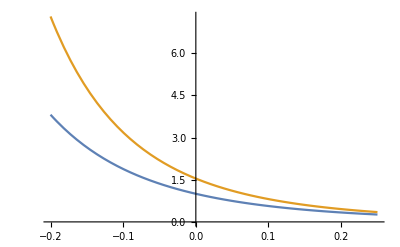

```mathematica
Et𝓋Primetp1Plot = Plot[
{𝓋Primetp1[𝒶t+𝓎bar],0.5 𝓋Primetp1[𝒶t+𝓎bar+η]+0.5 𝓋Primetp1[𝒶t+𝓎bar-η]}
,{𝒶t,ω-(𝒸min-.05),ω-𝒸max}
]
```

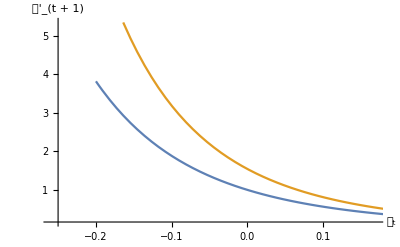

```mathematica
Et𝓋Primetp1Plot = Plot[
{𝓋Primetp1[𝒶t+𝓎bar],0.5 𝓋Primetp1[𝒶t+𝓎bar+η]+0.5 𝓋Primetp1[𝒶t+𝓎bar-η]}
,{𝒶t,ω-(𝒸min-.05),ω-𝒸max}
(*,Ticks->None*)
,AxesOrigin->{ω-(𝒸max+.05),uPrime[𝒸max]*.5}
,PlotRange->{{ω-(𝒸max*1.05),ω-(𝒸min+.03)},{uPrime[𝒸max]*0.5,uPrime[𝒸min]*1.4}}
,AxesLabel->{"𝒶_t","𝓋'_(t + 1)"}
]
```

```mathematica
uPrimePlot = Plot[
uPrime[ω-𝒶t]
,{𝒶t,ω - 𝒸min,ω-𝒸max}
(*,Ticks->None*)
,AxesOrigin->{ω-(𝒸max*1.02),uPrime[𝒸max]*.5}
,PlotRange->{{ω-(𝒸min-.3),ω-(𝒸max*1.02)},{uPrime[𝒸max]*.5,uPrime[𝒸min]*1.4}}
,AxesLabel->{"𝒶_t",""}];
```

```mathematica
𝒶PF = 𝒶CEQ[ω]
```

0.

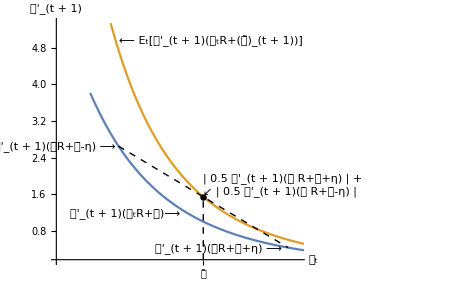

```mathematica
Et𝓋Primetp1 = Show[
Et𝓋Primetp1Plot
,Graphics[{Dashing[{.01}],Line[{{𝒶PF-η,𝓋Primetp1[𝒶PF+𝓎bar-η]},{𝒶PF+η,𝓋Primetp1[𝒶PF+𝓎bar+η]}}]}]
,Graphics[{PointSize[.01],Point[{𝒶PF,.5 𝓋Primetp1[𝒶PF+𝓎bar+η]+.5 𝓋Primetp1[𝒶PF+𝓎bar-η]}]}]
,Graphics[Text["⟵ E_t[𝓋'_(t + 1)(𝒶_tR+(𝓎̃)_(t + 1))]",{ω-(𝒸max-.05),1.3*𝓋Primetp1[ω+𝓎bar-𝒸max]},{-1,0}]]
,Graphics[Text["𝓋'_(t + 1)(𝒶_tR+𝓎̄)⟶",{ω-(𝒸max-.16),uPrime[𝒸max]*3.5},{1,0}]]
,Graphics[Text["𝓋'_(t + 1)(𝒶̄R+𝓎̄-η) ⟶",{𝒶PF-η-.005,𝓋Primetp1[𝒶PF+𝓎bar-η]},{1,0}]]
,Graphics[Text["𝓋'_(t + 1)(𝒶̄R+𝓎̄+η) ⟶",{𝒶PF+η-.01,𝓋Primetp1[𝒶PF+𝓎bar+η]*.95},{1,0}]]
,Graphics[Text[GridBox[{{" ","0.5𝓋'_(t + 1)(𝒶̄R+𝓎̄+η)","+"},{"↙","0.5𝓋'_(t + 1)(𝒶̄R+𝓎̄-η)"," "}}] //DisplayForm,{𝒶PF/2,.5 𝓋Primetp1[𝒶PF+𝓎bar+η]+.5 𝓋Primetp1[𝒶PF+𝓎bar-η]},{-1,-1}]]
,Graphics[{Dashing[{.01,.01}],Line[{{𝒶PF,uPrime[𝒸max]*.5},{𝒶PF,.5 𝓋Primetp1[𝒶PF+𝓎bar+η]+.5 𝓋Primetp1[𝒶PF+𝓎bar-η]}}]}]
,Ticks->{{{𝒶PF,"𝒶̄"}},{}}
,DisplayFunction->$DisplayFunction
,AxesOrigin->{ω-(𝒸max+.06),uPrime[𝒸max]*.5}
,AxesLabel->{"𝒶_t","𝓋'_(t + 1)"}
,ImageSize -> {72. 6.5, 72. 6.5/GoldenRatio}
]
```

```mathematica
Export["EtvPrimetp1.eps",Et𝓋Primetp1,"EPS"];
Export["EtvPrimetp1.svg",Et𝓋Primetp1,"SVG"];
Export["EtvPrimetp1.pdf",Et𝓋Primetp1,"PDF"];
Export["EtvPrimetp1.png",Et𝓋Primetp1,"PNG"];
```

EtvPrimetp1.eps

EtvPrimetp1.svg

EtvPrimetp1.pdf

EtvPrimetp1.png

```mathematica
"EtvPrimetp1.eps"
```

EtvPrimetp1.eps

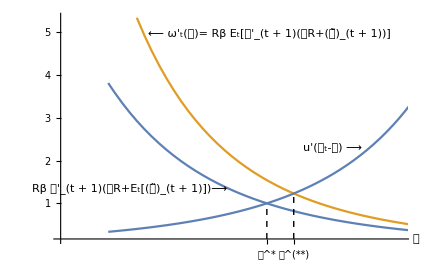

```mathematica
EquateMargUtils = Show[
Et𝓋Primetp1Plot
,uPrimePlot
,Graphics[{Dashing[{.01,.01}],Line[{{𝒶PF,uPrime[𝒸max]*.5},{𝒶PF,uPrime[ω-𝒶PF]}}]}]
,Graphics[{Dashing[{.01,.01}],Line[{{𝒶t[ω],uPrime[𝒸max]*.5},{𝒶t[ω],uPrime[𝒸t[ω]]}}]}]
,Graphics[Text["Rβ 𝓋'_(t + 1)(𝒶R+E_t[(𝓎̃)_(t + 1)])⟶",{ω-(𝒸max-.15),uPrime[𝒸max]*4},{1,0}]]
,Graphics[Text["⟵ ω'_t(𝒶)= Rβ E_t[𝓋'_(t + 1)(𝒶R+(𝓎̃)_(t + 1))]",{ω-(𝒸max-.05),1.3*𝓋Primetp1[ω+𝓎bar-𝒸max]},{-1,0}]]
,Graphics[Text["u'(𝓂_t-𝒶) ⟶",{ω-(𝒸min+.08),uPrime[ω-.13]},{1,0}]]
,AxesLabel->{"𝒶",""}
,Ticks->{{{𝒶t[ω],"𝒶^(**)"},{𝒶PF,"𝒶^*"}},{}}
,AxesOrigin->{ω-(𝒸max+.06),uPrime[𝒸max]*.5}
,ImageSize->{72. 6., 72. 6./GoldenRatio}
]
```

```mathematica
Export["EquateMargUtils.eps",EquateMargUtils,"EPS"];
Export["EquateMargUtils.pdf",EquateMargUtils,"PDF"];Export["EquateMargUtils.png",EquateMargUtils,"PNG"];Export["EquateMargUtils.svg",EquateMargUtils,"SVG"];
```